```mathematica
Clear["Global`*"]
dir=NotebookDirectory[];
K1=-7;
D1=-1.42;
K2=-1.5;
D2=-0.56;
K3=0.04;
D3=0.002;
m=0.086;
g=9.81;
J=1/12 m(0.02^2+0.035^2);
L=0.035;
(*u1max=1.224;
u2max=0.08925L;*)
Fmax=0.612;
scale=4050;
K1=-7;

(*Change between original and new controller*)
D1=-1.42;
K2=-1.5;(*Original:1.5, New:7*)
D2=-1.95;(*Original:1.95, New:3*)
(*Change between original and new controller*)

K3=.04;
D3=.002;
ωmax=19200/60*2π;
ωmin=10000/60*2π;
u11=m g+K1 (y[t]-yp[t])+D1( y'[t]-D[yp[t],t]);
(*ϕdes=Sign[K2 x[t]+D2 x'[t]]*Min[Abs[K2 x[t]+D2 x'[t]],0.2];*)
ϕdes=0.12Tanh[K2 (x[t]-xp[t])+D2 (x'[t]-D[xp[t],t])];
u21=K3(ϕdes-ϕ[t])+D3 (-ϕ'[t]);
(*Eredeti: u21=K3(ϕdes-ϕ[t])+D3 (D[ϕdes,t]-ϕ'[t]);*)
ω11=(u11+2 u21/L)/2 scale;
ω21=(u11-2 u21/L)/2 scale;
ω1=Max[Min[ω11,ωmax],ωmin];
ω2=Max[Min[ω21,ωmax],ωmin];
F1=lift[ω1,x'[t]Cos[ϕ[t]]+y'[t]Sin[ϕ[t]],-y'[t]Cos[ϕ[t]]-x'[t]Sin[ϕ[t]]-L*ϕ'[t]];
F2=lift[ω2,x'[t]Cos[ϕ[t]]+y'[t]Sin[ϕ[t]],-y'[t]Cos[ϕ[t]]-x'[t]Sin[ϕ[t]]+L*ϕ'[t]];
u1=F1+F2;
u2=L/2(F1-F2);

eqs={x''[t]==(u1 Sin[ϕ[t]])/m,y''[t]==-g+(u1 Cos[ϕ[t]])/m,ϕ''[t]==u2/J};
paramsnew={1.42,0.51,6.13,4,29.7,1.47};
paramsorig={7,1.42,1.5,1.95,0.04,0.002};
```

```mathematica
ComputeEqsSaturation[K1_,D1_,K2_,D2_,K3_,D3_]:=(
u11v=m g-K1 (y[t]-yp[t])-D1( y'[t]-D[yp[t],t]);
(*ϕdes=Sign[K2 x[t]+D2 x'[t]]*Min[Abs[K2 x[t]+D2 x'[t]],0.2];*)
ϕdesv=0.13Tanh[-K2 (x[t]-xp[t])-D2 (x'[t]-D[xp[t],t])];
u21v=K3(ϕdesv-ϕ[t])+D3 (-ϕ'[t]);
(*Eredeti: u21=K3(ϕdes-ϕ[t])+D3 (D[ϕdes,t]-ϕ'[t]);*)
ω1vv=Max[Min[(u11v+2 u21v/L)/2 scale,ωmax],ωmin];
ω2vv=Max[Min[(u11v-2 u21v/L)/2 scale,ωmax],ωmin];
F1v=lift[ω1vv,x'[t]Cos[ϕ[t]]+y'[t]Sin[ϕ[t]],-y'[t]Cos[ϕ[t]]-x'[t]Sin[ϕ[t]]-L*ϕ'[t]];
F2v=lift[ω2vv,x'[t]Cos[ϕ[t]]+y'[t]Sin[ϕ[t]],-y'[t]Cos[ϕ[t]]-x'[t]Sin[ϕ[t]]+L*ϕ'[t]];
u1v=F1v+F2v;
u2v=L/2(F1v-F2v);

Return[{x''[t]==(u1v Sin[ϕ[t]])/m,y''[t]==-g+(u1v Cos[ϕ[t]])/m,ϕ''[t]==u2v/J}])
ComputeOmega[K1_,D1_,K2_,D2_,K3_,D3_]:=(u11v=m g-K1 (y[t]-yp[t])-D1( y'[t]-D[yp[t],t]);
(*ϕdes=Sign[K2 x[t]+D2 x'[t]]*Min[Abs[K2 x[t]+D2 x'[t]],0.2];*)
ϕdesv=0.13Tanh[-K2 (x[t]-xp[t])-D2 (x'[t]-D[xp[t],t])];
u21v=K3(ϕdesv-ϕ[t])+D3 (-ϕ'[t]);
(*Eredeti: u21=K3(ϕdes-ϕ[t])+D3 (D[ϕdes,t]-ϕ'[t]);*)
ω1vvv=Max[Min[(u11v+2 u21v/L)/2 scale,ωmax],ωmin];
ω2vvv=Max[Min[(u11v-2 u21v/L)/2 scale,ωmax],ωmin];
Return[{ω1vvv,ω2vvv}])
(*Simulate the system with both lift models. The params for the lift model are in order: ω,vx,vy*)
liftnew[ω_,vx_,vy_]:=-2*(0.0005917217101953038 vx^2-0.00002557102446913359 vx^4-0.0009764562665337519 vy-0.00013859859899200091 vx^2 vy+0.00004560884655456854 vy^3-7.893807214858706*^-8 ω^2);
Simulate[xpa_,ypa_,T_,newcontr_,IC_:{1,0,0,0,0,0}]:=<|
"orig"->NDSolve[(ComputeEqsSaturation@@paramsorig/.{xp->xpa,yp->ypa,lift->liftnew})&&x[0]==IC[[1]]&&y[0]==IC[[2]]&&ϕ[0]==IC[[3]]&&x'[0]==IC[[4]]&&y'[0]==IC[[5]]&&ϕ'[0]==IC[[6]],{x[t],y[t],ϕ[t]},{t,0,T},InterpolationOrder->4][[1]],"new"->NDSolve[(ComputeEqsSaturation@@newcontr/.{xp->xpa,yp->ypa,lift->liftnew})&&x[0]==IC[[1]]&&y[0]==IC[[2]]&&ϕ[0]==IC[[3]]&&x'[0]==IC[[4]]&&y'[0]==IC[[5]]&&ϕ'[0]==IC[[6]],{x[t],y[t],ϕ[t]},{t,0,T},InterpolationOrder->4][[1]],"paramorig"->paramsorig,"paramnew"->newcontr|>
(*Plot omegas*)
PlotOmega[sol_,ranges_,onlyoneplot_:False,plotstyle_:{{Blue,Thickness[.008]},{Green,Thickness[.008]},{Red,Dashed,Thickness[.008]},{Orange,Dashed,Thickness[.008]}}]:=(ω1v=(ComputeOmega@@sol[["paramnew"]])[[1]]/.Flatten[{sol[["new"]],D[sol[["new"]],t],D[D[sol[["new"]],t],t],xp'[t]->D[xp[t],t],yp'[t]->D[yp[t],t]}];
ω1vorig=(ComputeOmega@@sol[["paramorig"]])[[1]]/.Flatten[{sol[["orig"]],D[sol[["orig"]],t],D[D[sol[["orig"]],t],t],xp'[t]->D[xp[t],t],yp'[t]->D[yp[t],t]}];
ω2v=(ComputeOmega@@sol[["paramnew"]])[[2]]/.Flatten[{sol[["new"]],D[sol[["new"]],t],D[D[sol[["new"]],t],t],xp'[t]->D[xp[t],t],yp'[t]->D[yp[t],t]}];
ω2vorig=(ComputeOmega@@sol[["paramorig"]])[[2]]/.Flatten[{sol[["orig"]],D[sol[["orig"]],t],D[D[sol[["orig"]],t],t],xp'[t]->D[xp[t],t],yp'[t]->D[yp[t],t]}];
ωplot1=Plot[{ω1v,ω1vorig,ω2v,ω2vorig},{t,ranges[[1,1]],ranges[[1,2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","ω [rad/s]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle,Exclusions->None];
ωplot2=Plot[{ω1v,ω1vorig,ω2v,ω2vorig},{t,ranges[[2,1]],ranges[[2,2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle,Exclusions->None];
Legended[Grid[If[!onlyoneplot,{{ωplot1,ωplot2}},{{ωplot1}}]],Placed[LineLegend[Directive@@@plotstyle,{"ω_1 Fine-tuned controller","ω_1 Original controller","ω_2 Fine-tuned controller","ω_2 Original controller"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},LegendLayout->"Row"],Below]])
Plotxy[sol_,range_,plotstyle_:{{Blue,Thickness[.008]},{Green,Thickness[.008],Dashing[Large,Large]},{Red,Dashing[Small,Medium],Thickness[.008]}}]:=(xplot=Plot[{x[t]/.sol[["new"]],x[t]/.sol[["orig"]],xp[t]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","x [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
yplot=Plot[{y[t]/.sol[["new"]],y[t]/.sol[["orig"]],yp[t]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","y [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
Legended[Grid[{{xplot,yplot}}],Placed[LineLegend[Directive@@@plotstyle,{"Fine-tuned controller","Original controller","Prescribed"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},LegendLayout->"Row"],Below]])
Plotxyϕ[sol_,range_,plotstyle_:{{Blue,Thickness[.008]},{Green,Thickness[.008],Dashing[Large,Large]},{Red,Dashing[Small,Medium],Thickness[.008]}}]:=(xplot=Plot[{x[t]/.sol[["new"]],x[t]/.sol[["orig"]],xp[t]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","x [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
yplot=Plot[{y[t]/.sol[["new"]],y[t]/.sol[["orig"]],yp[t]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","y [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
ϕplot=Plot[{ϕ[t]/.sol[["new"]],ϕ[t]/.sol[["orig"]]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","ϕ [rad]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
Legended[Grid[{{xplot,yplot},{ϕplot}}],Placed[LineLegend[Directive@@@plotstyle,{"Fine-tuned controller","Original controller","Prescribed"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},LegendLayout->"Row"],Below]])
Plottraj[sol_,range_,maxtimeprescribed_,plotstyle_:{{Blue,Thickness[.008]},{Green,Thickness[.008],Dashing[Large,Large]},{Red,Dashing[Small,Medium],Thickness[.008]}}]:=(ParametricPlot[{{x[t],y[t]}/.sol[["new"]],{x[t],y[t]}/.sol[["orig"]],Piecewise[{{{xp[t],yp[t]},t<maxtimeprescribed}},Indeterminate]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{HoldForm[x" [m]"],HoldForm[y" [m]"]},LabelStyle-> {Black,FontSize->36,FontFamily->"Times"},ImageSize->Large,AspectRatio->1,PlotLegends->{"Fine-tuned controller","Original controller","Prescribed"},PlotStyle->plotstyle])
```

```mathematica
L2Norm[fcn_,tmin_,tmax_]:=NIntegrate[fcn^2,{t,tmin,tmax},MaxRecursion->100]
NormedRMSE[fcn_,fcnp_,tmin_,tmax_]:=L2Norm[fcn-fcnp,tmin,tmax]/L2Norm[fcnp,tmin,tmax]
diff[sol_,xp_,yp_,maxtorig_,maxtnew_,mintorig_:0,mintnew_:0,dt_:10^-3]:=<|"orig,x"->NormedRMSE[x[t]/.sol[["orig"]],xp[t],mintorig,maxtorig],"new,x"->NormedRMSE[x[t]/.sol[["new"]],xp[t],mintnew,maxtnew],
"orig,y"->NormedRMSE[y[t]/.sol[["orig"]],yp[t],mintorig,maxtorig],"new,y"->NormedRMSE[y[t]/.sol[["new"]],yp[t],mintnew,maxtnew],
"orig,total"->√((NormedRMSE[x[t]/.sol[["orig"]],xp[t],mintorig,maxtorig])^2+(NormedRMSE[y[t]/.sol[["orig"]],yp[t],mintorig,maxtorig])^2),"new,total"->√((NormedRMSE[x[t]/.sol[["new"]],xp[t],mintnew,maxtnew])^2+(NormedRMSE[y[t]/.sol[["new"]],yp[t],mintnew,maxtnew])^2)|>*100
```

## Circle

## vel=0.2

<|orig,x→0.0403377,new,x→0.00253353,orig,y→0.00573917,new,y→0.138753,orig,total→0.0407439,new,total→0.138776|>

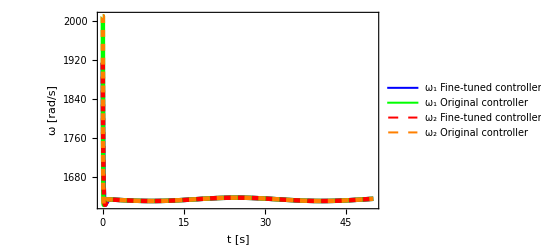

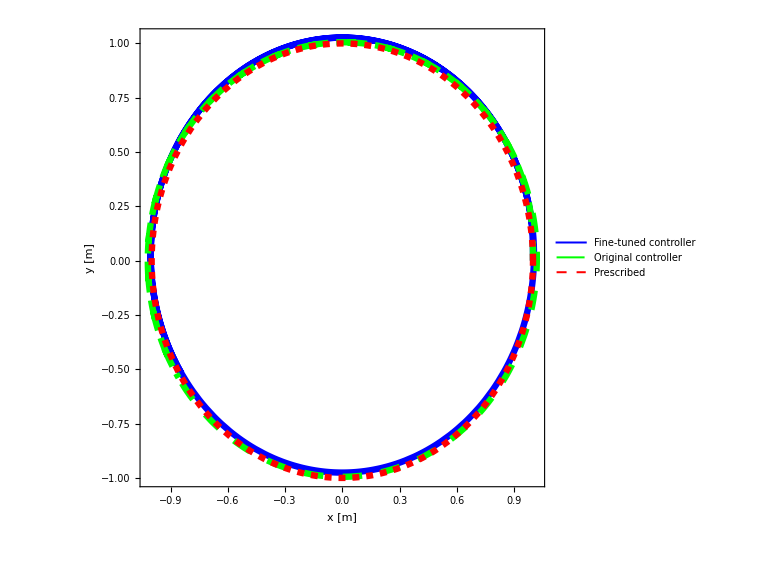

```mathematica
vel=0.2;
T=50;
xp[t_]:=Cos[vel t];
yp[t_]:=Sin[vel t];
sol=Simulate[xp[t],yp[t],T,paramsnew];
diff[sol,xp,yp,T,T]
pocv02=PlotOmega[sol,{{0,T},{11.06,11.08}},True]
ptcv02=Plottraj[sol,{0,T},2 π/vel]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_circle_new_omega02.png"}],pocv02,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_circle_new_traj02.png"}],ptcv02,ImageResolution->500];
```

## vel=0.5

<|orig,x→1.29215,new,x→0.0941912,orig,y→0.00718406,new,y→0.152739,orig,total→1.29217,new,total→0.179447|>

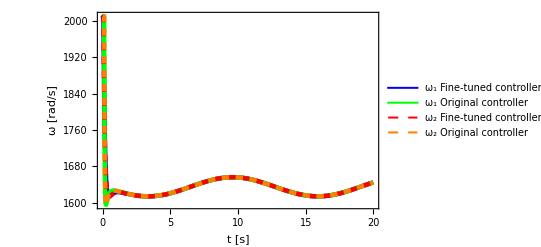

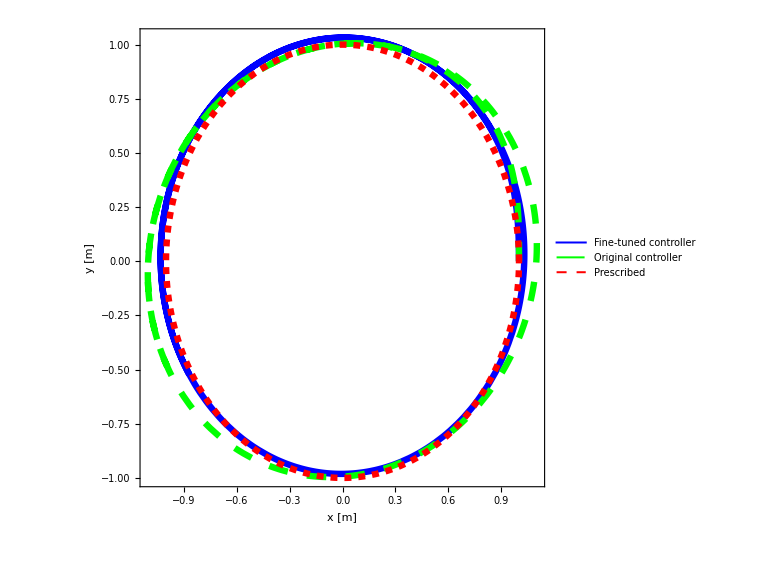

```mathematica
vel=0.5;
T=20;
xp[t_]:=Cos[vel t];
yp[t_]:=Sin[vel t];
sol=Simulate[xp[t],yp[t],T,paramsnew];
diff[sol,xp,yp,T,T]
pocv05=PlotOmega[sol,{{0,T},{2,20}},True]
ptcv05=Plottraj[sol,{0,T},2 π/vel]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_circle_new_omega05.png"}],pocv05,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_circle_new_traj05.png"}],ptcv05,ImageResolution->500];
```

## vel=1

<|orig,x→23.1723,new,x→2.3595,orig,y→0.0570025,new,y→0.297499,orig,total→23.1724,new,total→2.37818|>

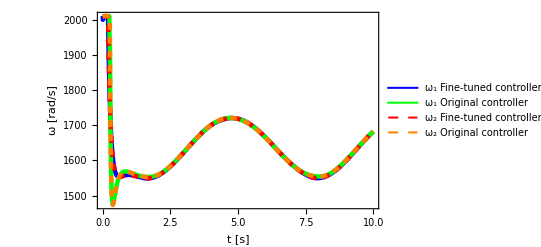

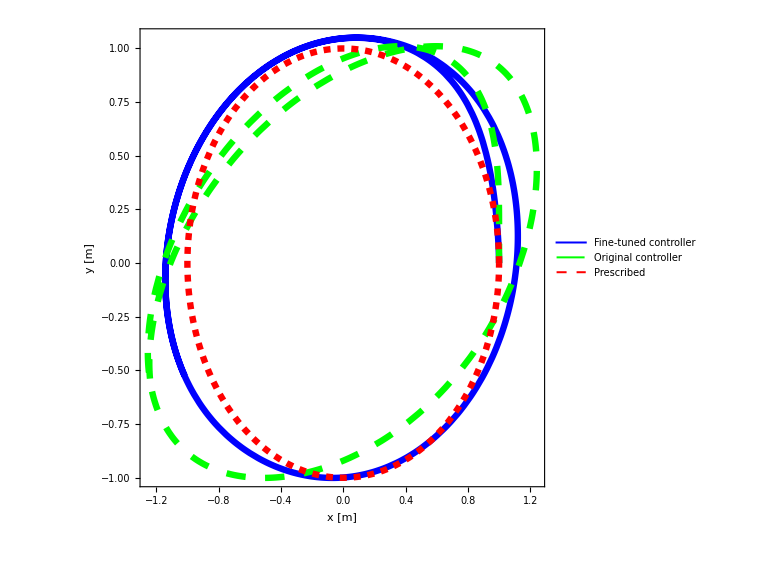

```mathematica
vel=1;
T=10;
xp[t_]:=Cos[vel t];
yp[t_]:=Sin[vel t];
sol=Simulate[xp[t],yp[t],T,paramsnew];
diff[sol,xp,yp,T,T]
pocv1=PlotOmega[sol,{{0,T},{2,20}},True]
ptcv1=Plottraj[sol,{0,T},2 π/vel]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_circle_new_omega1.png"}],pocv1,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_circle_new_traj1.png"}],ptcv1,ImageResolution->500];
```

## Discontinous/sine

## v=1

### SD

<|orig,x→24.8218,new,x→7.19565,orig,y→43.9966,new,y→47.219,orig,total→50.5156,new,total→47.7641|>

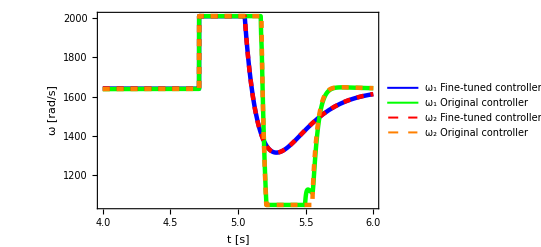

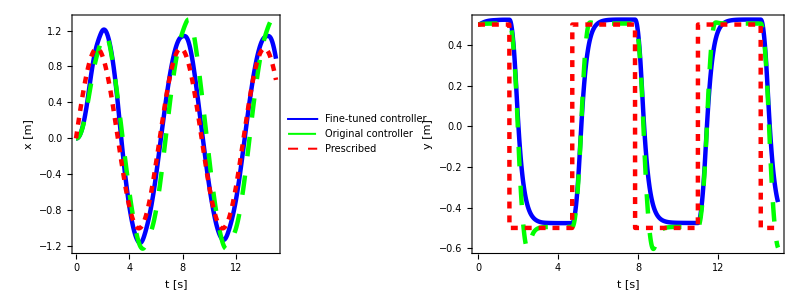

```mathematica
vel=1;
xp[t_]:=Sin[vel t];
yp[t_]:=Piecewise[{{0.5,Cos[vel t]>0},{-0.5,Cos[vel t]<0}}];
T=15;
sol=Simulate[xp[t],yp[t],T,paramsnew,{0,0.5,0,0,0,0}];
diff[sol,xp,yp,T,T]
polv1=PlotOmega[sol,{{4,6},{2,T}},True]
pxylv1=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_Linear_new_omega1.png"}],polv1,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_Linear_new_disp1.png"}],pxylv1,ImageResolution->500];
```

### DS

<|orig,x→117.707,new,x→97.4166,orig,y→0.0381496,new,y→0.246672,orig,total→117.707,new,total→97.4169|>

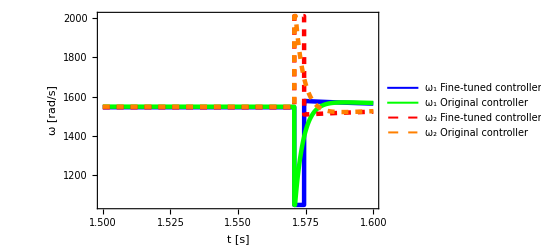

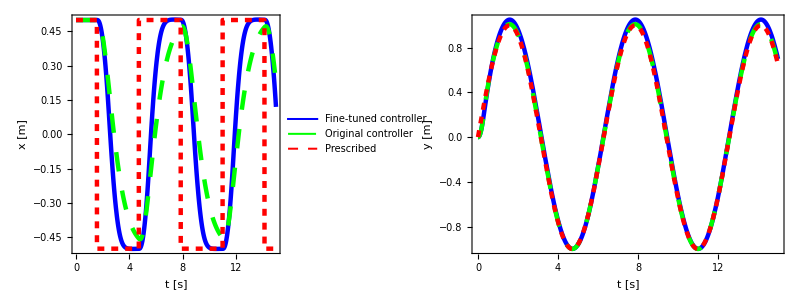

```mathematica
vel=1;
xp[t_]:=Piecewise[{{0.5,Cos[vel t]>0},{-0.5,Cos[vel t]<0}}];
yp[t_]:=Sin[vel t];
T=15;
sol=Simulate[xp[t],yp[t],T,paramsnew,{0.5,0,0,0,0,0}];
diff[sol,xp,yp,T,T]
podsv1=PlotOmega[sol,{{1.5,1.6},{2,T}},True]
pxydsv1=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_ds_new_disp1.png"}],pxydsv1,ImageResolution->500];
```

### DD

<|orig,x→136.73,new,x→86.6202,orig,y→37.1072,new,y→42.5271,orig,total→141.676,new,total→96.4967|>

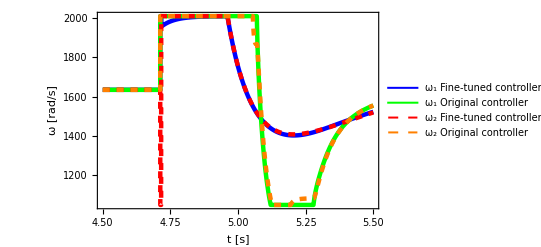

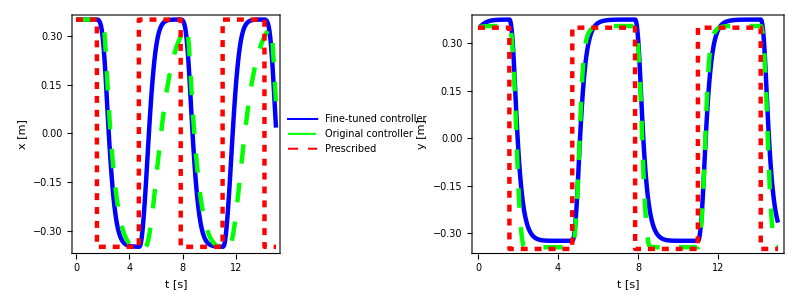

```mathematica
vel=1;
A=0.35;
xp[t_]:=Piecewise[{{A,Cos[vel t]>0},{-A,Cos[vel t]<0}}];
yp[t_]:=Piecewise[{{A,Cos[vel t]>0},{-A,Cos[vel t]<0}}];
T=15;
sol=Simulate[xp[t],yp[t],T,paramsnew,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
poddv1=PlotOmega[sol,{{4.5,5.5},{2,T}},True]
pxyddv1=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_dd_new_disp1.png"}],pxyddv1,ImageResolution->500];
```

## v=1.5

### SD

<|orig,x→466.925,new,x→235.589,orig,y→61.9109,new,y→66.2213,orig,total→471.011,new,total→244.719|>

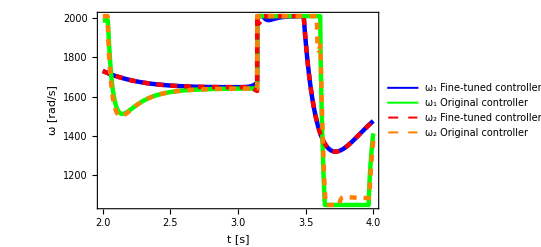

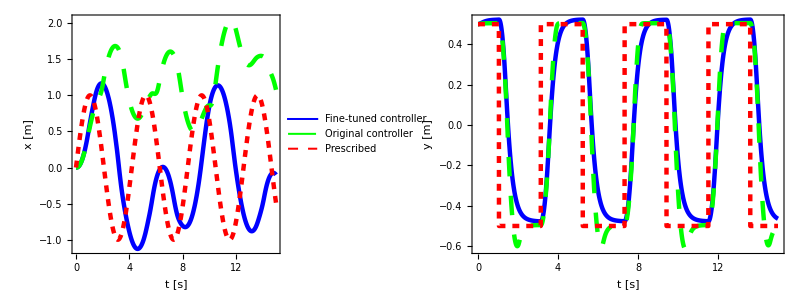

```mathematica
vel=1.5;
xp[t_]:=Sin[vel t];
yp[t_]:=Piecewise[{{0.5,Cos[vel t]>0},{-0.5,Cos[vel t]<0}}];
T=15;
sol=Simulate[xp[t],yp[t],T,paramsnew,{0,0.5,0,0,0,0}];
diff[sol,xp,yp,T,T]
polv15=PlotOmega[sol,{{2,4},{2,T}},True]
pxylv15=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_Linear_new_omega15.png"}],polv15,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_Linear_new_disp15.png"}],pxylv15,ImageResolution->500];
```

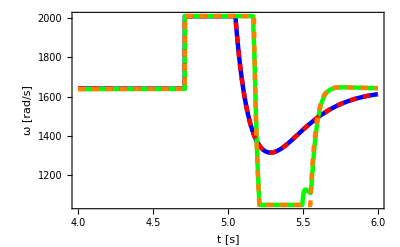

```mathematica
First@polv1
```

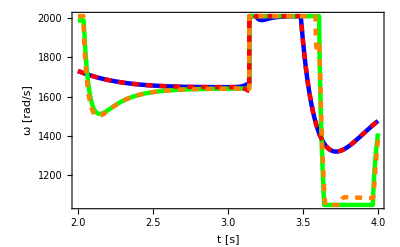
-Graphics- | -Graphics-

```mathematica
polvall=Legended[Grid[{First/@{polv1,polv15}}],Last@polv1]
Export[FileNameJoin[{dir,"fig/out_Linear_new_omegaall.png"}],polvall,ImageResolution->500];
```

### DS

<|orig,x→151.403,new,x→147.201,orig,y→0.206455,new,y→0.73337,orig,total→151.403,new,total→147.202|>

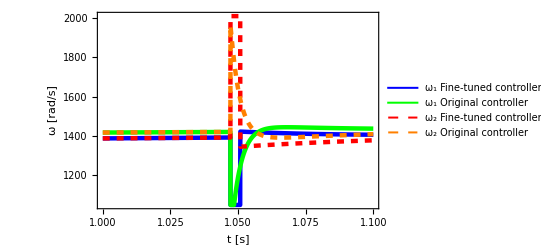

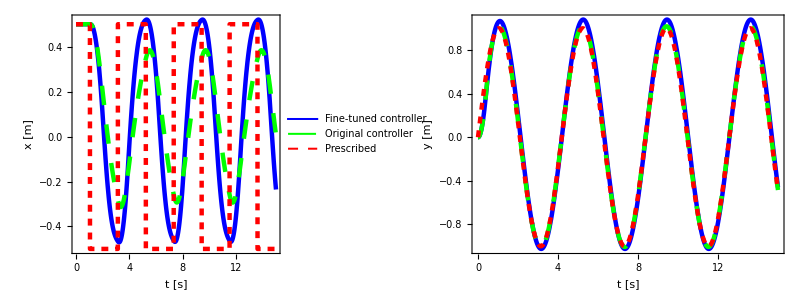

```mathematica
vel=1.5;
xp[t_]:=Piecewise[{{0.5,Cos[vel t]>0},{-0.5,Cos[vel t]<0}}];
yp[t_]:=Sin[vel t];
T=15;
sol=Simulate[xp[t],yp[t],T,paramsnew,{0.5,0,0,0,0,0}];
diff[sol,xp,yp,T,T]
podsv15=PlotOmega[sol,{{1,1.1},{2,T}},True]
pxydsv15=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_ds_new_disp15.png"}],pxydsv15,ImageResolution->500];
```

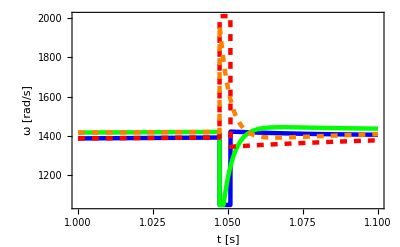
-Graphics- | -Graphics-

```mathematica
podsvall=Legended[Grid[{First/@{podsv1,podsv15}}],Last@podsv1]
Export[FileNameJoin[{dir,"fig/out_ds_new_omegaall.png"}],podsvall,ImageResolution->500];
```

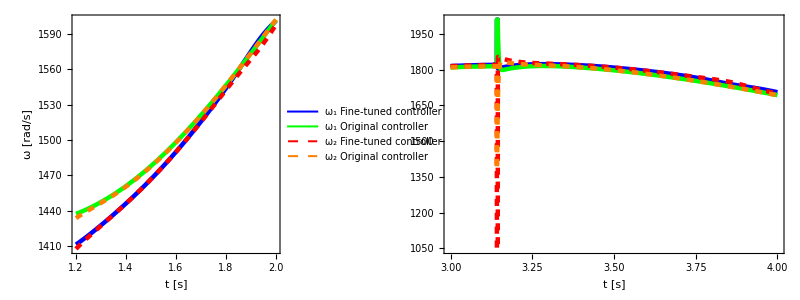

```mathematica
poddv15=PlotOmega[sol,{{1.2,2},{3,4}},False]
```

### DD

<|orig,x→171.943,new,x→123.262,orig,y→51.9841,new,y→59.0709,orig,total→179.63,new,total→136.686|>

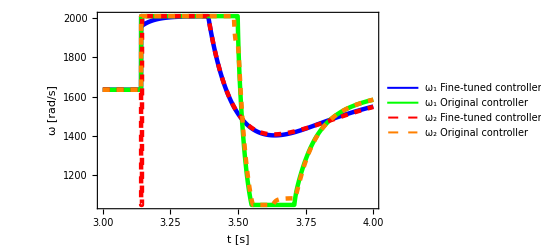

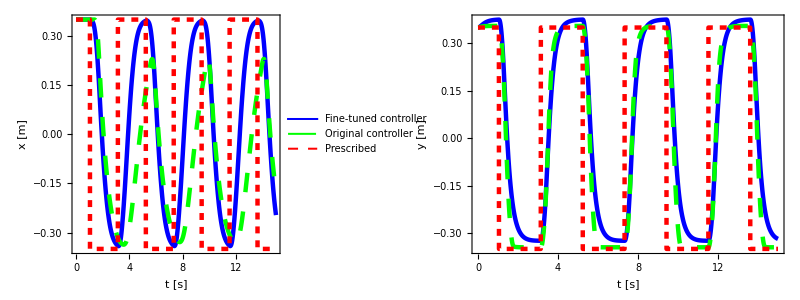

```mathematica
vel=1.5;
A=0.35;
xp[t_]:=Piecewise[{{A,Cos[vel t]>0},{-A,Cos[vel t]<0}}];
yp[t_]:=Piecewise[{{A,Cos[vel t]>0},{-A,Cos[vel t]<0}}];
T=15;
sol=Simulate[xp[t],yp[t],T,paramsnew,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
poddv15=PlotOmega[sol,{{3,4},{2,T}},True]
pxyddv15=Plotxy[sol,{0,T}]
```

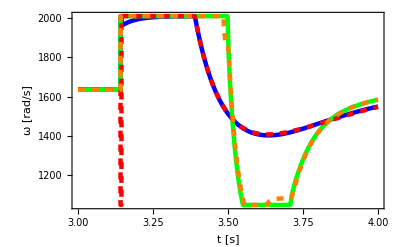
-Graphics- | -Graphics-

```mathematica
Export[FileNameJoin[{dir,"fig/out_dd_new_disp15.png"}],pxyddv15,ImageResolution->500];
poddvall=Legended[Grid[{First/@{poddv1,poddv15}}],Last@poddv1]
Export[FileNameJoin[{dir,"fig/out_dd_new_omegaall.png"}],poddvall,ImageResolution->500];
```

## Piecewise linear square

## vel=1

### a=0.4

<|orig,x→193.712,new,x→89.6917,orig,y→16.9393,new,y→15.2837,orig,total→194.451,new,total→90.9846|>

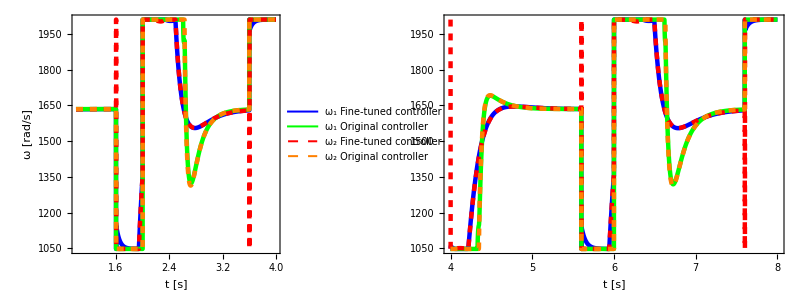

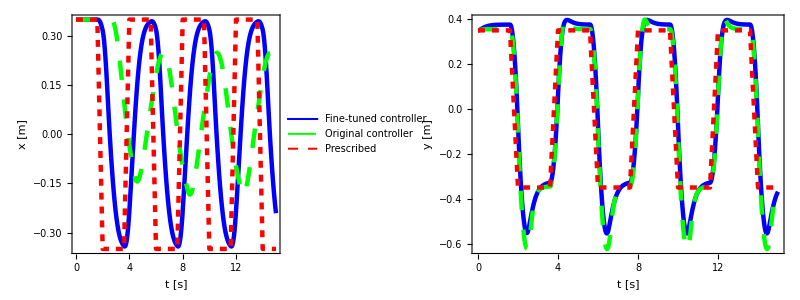

```mathematica
vel=1;
A=0.35;
a=0.4;
xp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1]
yp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1];
T=15;
sol=Simulate[xp[t],yp[t],T,paramsnew,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
popla04=PlotOmega[sol,{{1,4},{4,8}}]
pxypla04=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_pl_new_disp04.png"}],pxypla04,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_pl_new_omega04.png"}],popla04,ImageResolution->500];
```

### a=0.35

<|orig,x→184.079,new,x→92.9276,orig,y→14.9296,new,y→16.9421,orig,total→184.684,new,total→94.4593|>

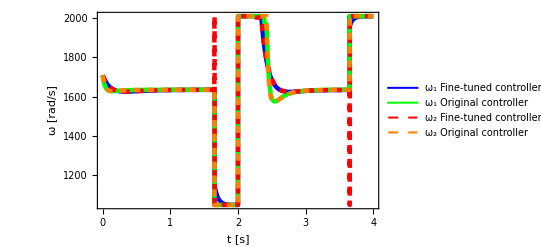

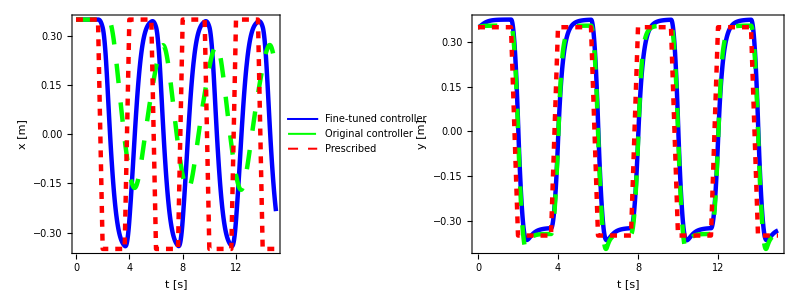

```mathematica
vel=1;
A=0.35;
a=0.35;
xp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1]
yp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1];
T=15;
sol=Simulate[xp[t],yp[t],T,paramsnew,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
popla035=PlotOmega[sol,{{0,4},{2,T}},True]
pxypla035=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_pl_new_disp035.png"}],pxypla035,ImageResolution->500];
```

### a=0.3

<|orig,x→152.635,new,x→96.1345,orig,y→19.6994,new,y→25.0693,orig,total→153.901,new,total→99.3494|>

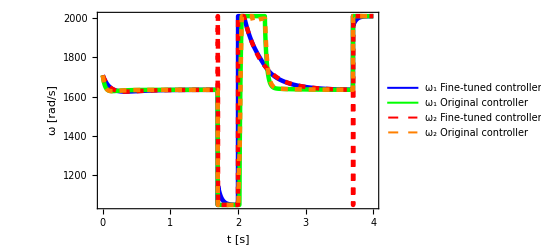

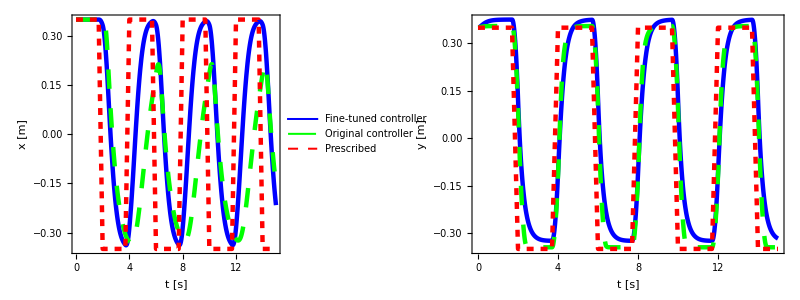

```mathematica
vel=1;
A=0.35;
a=0.3;
xp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1]
yp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1];
T=15;
sol=Simulate[xp[t],yp[t],T,paramsnew,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
popla03=PlotOmega[sol,{{0,4},{2,T}},True]
pxypla03=Plotxy[sol,{0,T}]
```

```mathematica
popl=Legended[Grid[{First/@{popla035,popla03}}],Last@popla03];
Export[FileNameJoin[{dir,"fig/out_pl_new_disp03.png"}],pxypla03,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_pl_new_omega.png"}],popl,ImageResolution->500];
```

## Piecewise linear square phase shift

### a=0.4

<|orig,x→86.39,new,x→85.1332,orig,y→15.1468,new,y→13.8384,orig,total→87.7078,new,total→86.2506|>

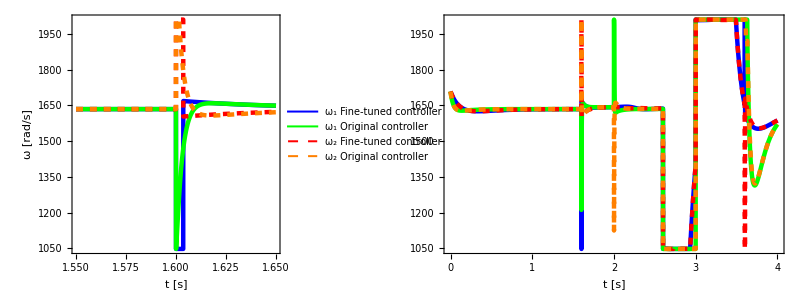

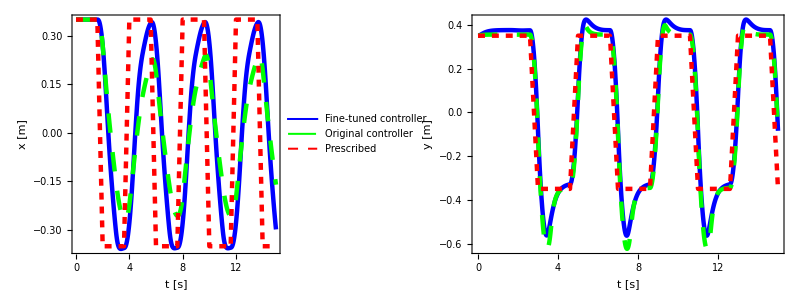

```mathematica
vel=1;
A=0.35;
a=0.4;
xp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1]
yp[t_]:=Interpolation[Flatten[{{{{0,A}}},Table[{{2 i/vel+1,(-1)^i A},{2(i+1)/vel+1-a,(-1)^i A}},{i,0,IntegerPart[T/2]}]},2],t,InterpolationOrder->1];
T=15;
sol=Simulate[xp[t],yp[t],T,paramsnew,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
poplpa04=PlotOmega[sol,{{1.55,1.65},{0,4}}]
pxyplpa04=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_plp_new_disp04.png"}],pxyplpa04,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_plp_new_omega04.png"}],poplpa04,ImageResolution->500];
```

### a=0.35

<|orig,x→95.3535,new,x→89.2019,orig,y→14.3841,new,y→15.1599,orig,total→96.4323,new,total→90.4809|>

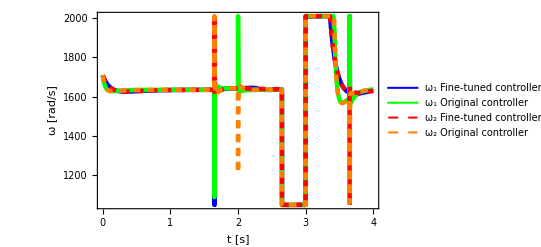

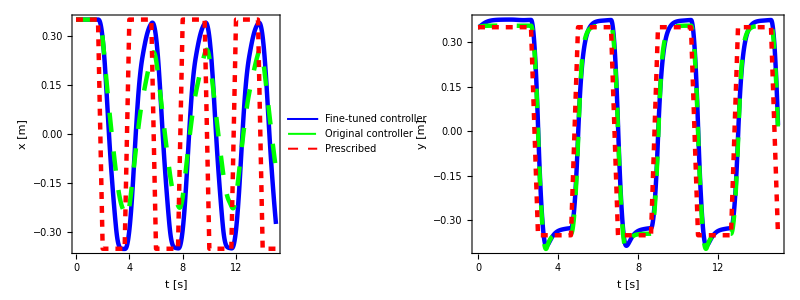

```mathematica
vel=1;
A=0.35;
a=0.35;
xp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1]
yp[t_]:=Interpolation[Flatten[{{{{0,A}}},Table[{{2 i/vel+1,(-1)^i A},{2(i+1)/vel+1-a,(-1)^i A}},{i,0,IntegerPart[T/2]}]},2],t,InterpolationOrder->1];
T=15;
sol=Simulate[xp[t],yp[t],T,paramsnew,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
poplpa035=PlotOmega[sol,{{0,4},{2,T}},True]
pxyplpa035=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_plp_new_disp035.png"}],pxyplpa035,ImageResolution->500];
```

### a=0.3

<|orig,x→102.648,new,x→93.6192,orig,y→18.6363,new,y→21.8534,orig,total→104.326,new,total→96.1359|>

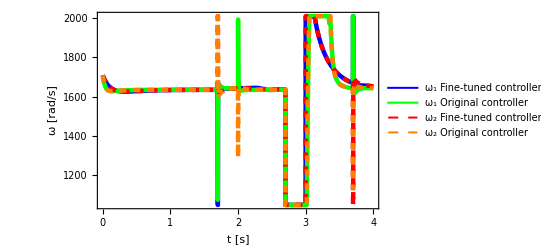

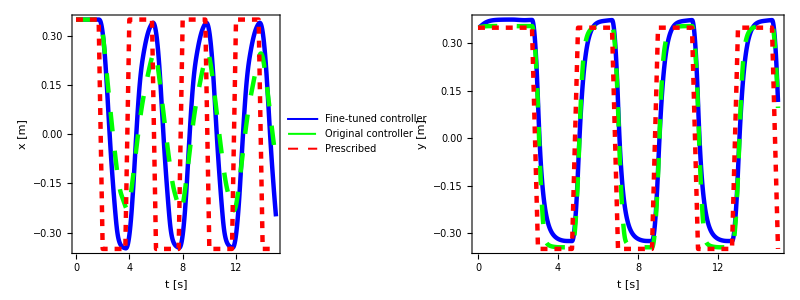

```mathematica
vel=1;
A=0.35;
a=0.3;
xp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1]
yp[t_]:=Interpolation[Flatten[{{{{0,A}}},Table[{{2 i/vel+1,(-1)^i A},{2(i+1)/vel+1-a,(-1)^i A}},{i,0,IntegerPart[T/2]}]},2],t,InterpolationOrder->1];
T=15;
sol=Simulate[xp[t],yp[t],T,paramsnew,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
poplpa03=PlotOmega[sol,{{0,4},{2,T}},True]
pxyplpa03=Plotxy[sol,{0,T}]
```

```mathematica
poplp=Legended[Grid[{First/@{poplpa035,poplpa03}}],Last@poplpa03];
Export[FileNameJoin[{dir,"fig/out_plp_new_disp03.png"}],pxyplpa03,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_plp_new_omega.png"}],poplp,ImageResolution->500];
```

## Smooth

## Smooth1

<|orig,x→61.2709,new,x→4.29553,orig,y→0.131109,new,y→0.11047,orig,total→61.271,new,total→4.29695|>

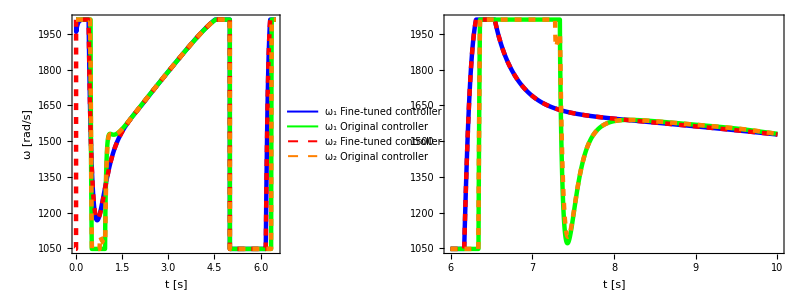

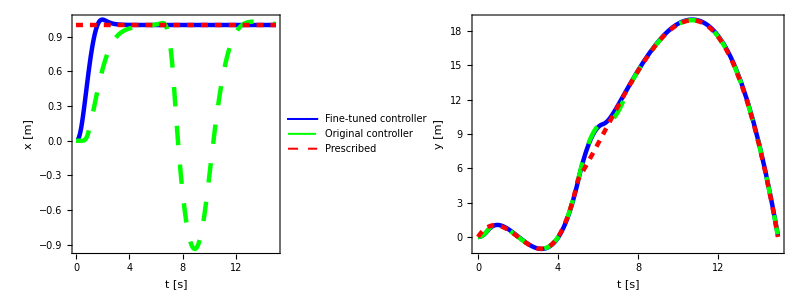

```mathematica
vel=1;
A=0.35;
a=0.3;
xp[t_]:=1;
yp[t_]:=Interpolation[{{0,0},{1,1},{2,0},{5,5},{15,0}},t] ;
T=15;
sol=Simulate[xp[t],yp[t],T,paramsnew,{0,0,0,0,0,0}];
diff[sol,xp,yp,T,T]
posm1=PlotOmega[sol,{{0,6.5},{6,10}}]
pxysm1=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_sm1_new_disp.png"}],pxysm1,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_sm1_new_omega.png"}],posm1,ImageResolution->500];
```

## Smooth2

<|orig,x→0.182558,new,x→0.0386083,orig,y→60.5957,new,y→78.5239,orig,total→60.5959,new,total→78.5239|>

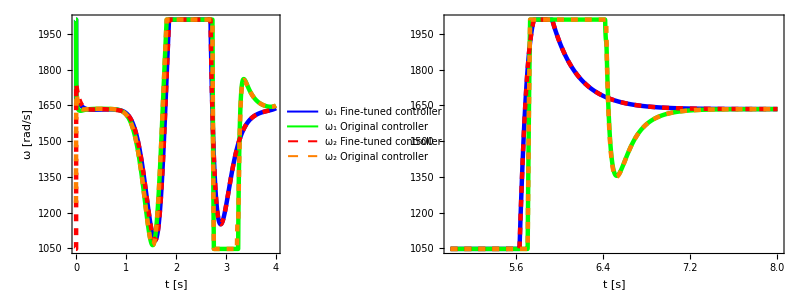

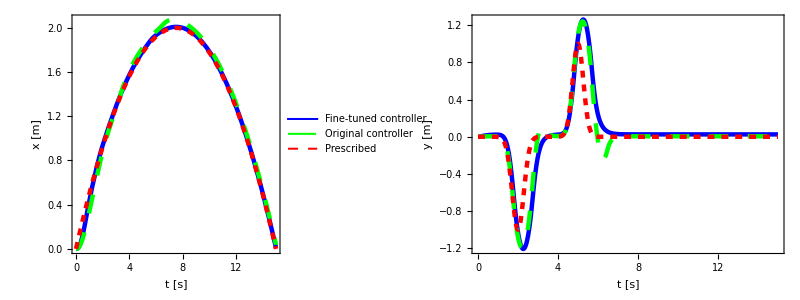

```mathematica
vel=1;
A=0.35;
a=6;
b=7;
xp[t_]:=(-(t-7.5)^2/7.5^2+1)*2;
yp[t_]:=-ⅇ^(-a*(t-2)^2)+ⅇ^(-b*(t-5)^2);
T=15;
sol=Simulate[xp[t],yp[t],T,paramsnew,{0,0,0,0,0,0}];
diff[sol,xp,yp,T,T]
posm2=PlotOmega[sol,{{0,4},{5,8}}]
pxysm2=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_sm2_new_disp.png"}],pxysm2,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_sm2_new_omega.png"}],posm2,ImageResolution->500];
```